# Изпит

## Задача 1

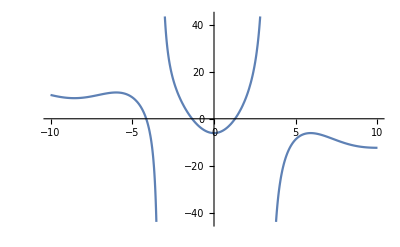

```mathematica
f[x_]:=(-45*2Cos[x]+x^3+23)/(11-x^2)
Plot[f[x], {x, -10, 10}]
```

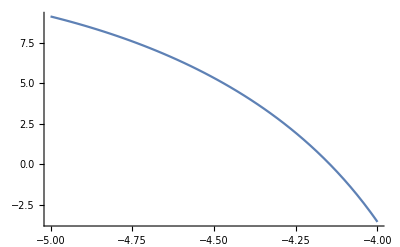

```mathematica
Plot[f[x], {x, -5, -4}]
```

```mathematica
a=-5.; b=-4.;
For[n=0,n≤3,n++
Print["n = ",n," a = ",a," b = ",b," m = ",m=(a+b)/2," f(m) = ",f[m]," ε = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 1 a = -5. b = -4. m = -4.5 f(m) = 5.31388 ε = 0.5

n = 2 a = -5. b = -4.5 m = -4.75 f(m) = 7.57242 ε = 0.25

n = 3 a = -5. b = -4.75 m = -4.875 f(m) = 8.41541 ε = 0.125

n = 4 a = -5. b = -4.875 m = -4.9375 f(m) = 8.7795 ε = 0.0625

```mathematica
a=-5.; b=-4.;
epszad=0.00001;
eps=10; (*произволна стойност по-голяма от предварително зададената грешка*)
For[n=0, eps > epszad,n++
Print["n = ",n," a = ",SetPrecision[a,12]," b = ",SetPrecision[b,12]," m = ",m= SetPrecision[m = (a+b)/2, 12]," f(m) = ",f[m]," ε = ",eps = (b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 1 a = -5. b = -4. m = -4.5 f(m) = 5.313878708 ε = 0.5

n = 2 a = -5. b = -4.5 m = -4.75 f(m) = 7.572416758 ε = 0.25

n = 3 a = -5. b = -4.75 m = -4.875 f(m) = 8.415412611 ε = 0.125

n = 4 a = -5. b = -4.875 m = -4.9375 f(m) = 8.779504079 ε = 0.0625

n = 5 a = -5. b = -4.9375 m = -4.96875 f(m) = 8.948509636 ε = 0.03125

n = 6 a = -5. b = -4.96875 m = -4.984375 f(m) = 9.029896284 ε = 0.015625

n = 7 a = -5. b = -4.984375 m = -4.9921875 f(m) = 9.0698275049 ε = 0.0078125

n = 8 a = -5. b = -4.9921875 m = -4.99609375 f(m) = 9.089604644 ε = 0.00390625

n = 9 a = -5. b = -4.99609375 m = -4.998046875 f(m) = 9.0994463489 ε = 0.00195313

n = 10 a = -5. b = -4.998046875 m = -4.9990234375 f(m) = 9.1043555167 ε = 0.000976563

n = 11 a = -5. b = -4.9990234375 m = -4.99951171875 f(m) = 9.1068071833 ε = 0.000488281

n = 12 a = -5. b = -4.99951171875 m = -4.99975585938 f(m) = 9.1080322878 ε = 0.000244141

n = 13 a = -5. b = -4.99975585938 m = -4.99987792969 f(m) = 9.1086446579 ε = 0.00012207

n = 14 a = -5. b = -4.99987792969 m = -4.99993896484 f(m) = 9.1089507974 ε = 0.0000610352

n = 15 a = -5. b = -4.99993896484 m = -4.99996948242 f(m) = 9.1091038558 ε = 0.0000305176

n = 16 a = -5. b = -4.99996948242 m = -4.99998474121 f(m) = 9.1091803821 ε = 0.0000152588

n = 17 a = -5. b = -4.99998474121 m = -4.99999237061 f(m) = 9.1092186446 ε = 7.62939×10^-6

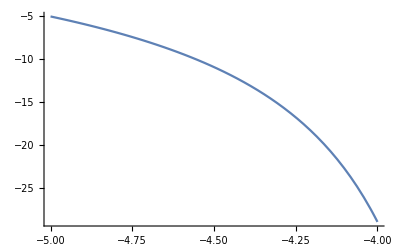

```mathematica
Plot[f'[x],{x,-5,-4}]
```

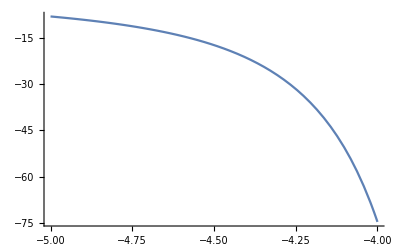

```mathematica
Plot[f''[x],{x,-5,-4}]
```

## Задача 2

```mathematica
A=({{2, 0, 2, 0}, {0, 4, 10, -9}, {3, 2, 1, 10}})
```

{{2,0,2,0},{0,4,10,-9},{3,2,1,10}}

```mathematica
(*Първа стъпка*)
(*Първи етап*)
A⟦1⟧=A⟦1⟧/A⟦1,1⟧
```

{1,0,1,0}

```mathematica
(*Втори ред*)
A⟦2⟧=A⟦2⟧-A⟦1⟧*A⟦2,1⟧
(*Трети ред*)
A⟦3⟧=A⟦3⟧-A⟦1⟧*A⟦3,1⟧
```

{0,4,10,-9}

{0,2,-2,10}

```mathematica
(*Втора стъпка*)
(*Първи етап*)
A⟦2⟧=A⟦2⟧/A⟦2,2⟧
(*Първи ред*)
A⟦1⟧=A⟦1⟧-A⟦2⟧*A⟦1,2⟧
(*Трети ред*)
i=3;j=2;
A⟦i⟧=A⟦i⟧-A⟦j⟧*A⟦i,j⟧
```

{0,1,5/2,-9/4}

{1,0,1,0}

{0,0,-7,29/2}

```mathematica
(*Трета стъпка*)
(*Първи етап*)
i=3;
A⟦i⟧=A⟦i⟧/A⟦i,i⟧
(*Втори етап*)
(*Първи ред*)
i=1;j=3;
A⟦i⟧=A⟦i⟧-A⟦j⟧*A⟦i,j⟧
(*Втори ред*)
i=2;j=3;
A⟦i⟧=A⟦i⟧-A⟦j⟧*A⟦i,j⟧
A//MatrixForm
```

{0,0,1,-29/14}

{1,0,0,29/14}

{0,1,0,41/14}

(1 | 0 | 0 | 29/14
0 | 1 | 0 | 41/14
0 | 0 | 1 | -29/14)

```mathematica
A=({{2, 0, 2, 0}, {0, 4, 10, -9}, {3, 2, 1, 10}})
n=Length[A];
deter=1;
For[j=1,j≤n,j++,deter=deter*A⟦j,j⟧;
A⟦j⟧=A⟦j⟧/A⟦j,j⟧; (*първи етап-получаване на единицата*)
For[i=1,i≤n,i++,If[i≠j,A⟦i⟧=A⟦i⟧-A⟦j⟧*A⟦i,j⟧ (*втори етап-получаване на нулите*)]];
Print[A//MatrixForm]
]
Print["Детерминантата на матрицата А е ",deter]
```

{{2,0,2,0},{0,4,10,-9},{3,2,1,10}}

(1 | 0 | 1 | 0
0 | 4 | 10 | -9
0 | 2 | -2 | 10)

(1 | 0 | 1 | 0
0 | 1 | 5/2 | -9/4
0 | 0 | -7 | 29/2)

(1 | 0 | 0 | 29/14
0 | 1 | 0 | 41/14
0 | 0 | 1 | -29/14)

Детерминантата на матрицата А е -56

```mathematica
A=({{2, 0, 2, 0, 1, 0, 0}, {0, 4, 10, -9, 0, 1, 0}, {3, 2, 1, 10, 0, 0, 1}});
n=Length[A];
deter=1;
For[j=1,j≤n,j++,deter=deter*A⟦j,j⟧;
A⟦j⟧=A⟦j⟧/A⟦j,j⟧; (*първи етап-получаване на единицата*)
For[i=1,i≤n,i++,If[i≠j,A⟦i⟧=A⟦i⟧-A⟦j⟧*A⟦i,j⟧ (*втори етап-получаване на нулите*)]];
Print[A//MatrixForm]
]
Print["Детерминантата на матрицата А е ",deter]
```

(1 | 0 | 1 | 0 | 1/2 | 0 | 0
0 | 4 | 10 | -9 | 0 | 1 | 0
0 | 2 | -2 | 10 | -3/2 | 0 | 1)

(1 | 0 | 1 | 0 | 1/2 | 0 | 0
0 | 1 | 5/2 | -9/4 | 0 | 1/4 | 0
0 | 0 | -7 | 29/2 | -3/2 | -1/2 | 1)

(1 | 0 | 0 | 29/14 | 2/7 | -1/14 | 1/7
0 | 1 | 0 | 41/14 | -15/28 | 1/14 | 5/14
0 | 0 | 1 | -29/14 | 3/14 | 1/14 | -1/7)

Детерминантата на матрицата А е -56

## Задача 3

```mathematica
xt=Table[10+9+i(0.3),{i,0,10}];
f[x_]:=(-45*2Cos[x]+x^3+23)/(11-x^2)
yt=f[xt]
bigN=Length[xt]
```

{-19.4086,-19.7268,-20.063,-20.4121,-20.768,-21.1247,-21.4763,-21.8178,-22.1453,-22.4565,-22.7505}

11

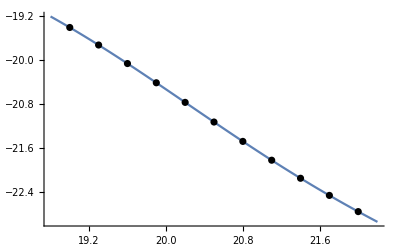

```mathematica
grf=Plot[f[x],{x,xt⟦1⟧-0.2,xt⟦bigN⟧+0.2}];
points=Table[{xt⟦i⟧,yt⟦i⟧},{i,1,bigN}];
grp=ListPlot[points,PlotStyle->Black];
Show[grf,grp]
```

```mathematica
b=-19.4086;
a=-22.7505;
n=bigN;
h=(b-a)/n;
I1=h*∑_(i=0)^(n-1) f[a+i*h];
M1=Abs[f'[b]];
R1=(b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ",h," и брой подинтервали n = ",n]
Print["Приблежената стойност по метода на левите правоъгълници е ",I1]
Print["Теоретичната грешка по метода на левите правоъгълници е ",R1]
```

Мрежата е със стъпка h = 0.303809 и брой подинтервали n = 11

Приблежената стойност по метода на левите правоъгълници е 72.2907

Теоретичната грешка по метода на левите правоъгълници е 0.417344

## Задача 4

```mathematica
DSolve[y'[x]==y[x]-Log[x^2+1]+(2x)/(x^2+1)+9,y[x],x]
```

DSolve::dsvar: 1.02 cannot be used as a variable.

DSolve[0==9.28666+41.6307[1.02],41.6307[1.02],1.02]

```mathematica
DSolve[{y'[x]==y[x]-Log[x^2+1]+(2x)/(x^2+1)+9, y[0]==9},y[x],x]
```

DSolve::dsvar: 1.02 cannot be used as a variable.

DSolve[{0==9.28666+41.6307[1.02],41.6307[0]==9},41.6307[1.02],1.02]

```mathematica
(*въвеждаме условието на задачата*)
a=0.;b=1;
x=a;
y=9.;
f[x_,y_]:=y-Log[x^2+1]+(2x)/(x^2+1)+9;
(*съставяме мрежата*)
n=4;h=(b-a)/n;
Print["Мрежата е с n = ",n," и стъпка h = ",h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка е ",h2]
Print["Теоретичната глобална грешка е ",h]
(*намираме неизвестните стойности за yi*)
For[i=0,i≤n,i++,
Print["i = ",i," xi = ",x," yi = ",y," fi = ",f[x,y]];
y=y+h*f[x,y];
x=x+h
]
```

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална грешка е h2

Теоретичната глобална грешка е 0.25

i = 0 xi = 0. yi = 9. fi = 18.

i = 1 xi = 0.25 yi = 13.5 fi = 22.91

i = 2 xi = 0.5 yi = 19.2275 fi = 28.8043

i = 3 xi = 0.75 yi = 26.4286 fi = 35.9423

i = 4 xi = 1. yi = 35.4142 fi = 44.721

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0 xi = 0. yi = 9. k1 = 0.36 k2 = 0.363998 k3 = 0.364038 k4 = 0.368072 yточно = Indeterminate истинска грешка = Indeterminate

i = 1 xi = 0.02 yi = 9.36402 k1 = 0.368072 k2 = 0.372142 k3 = 0.372183 k4 = 0.37629 yточно = -0.0782405 истинска грешка = 9.44226

i = 2 xi = 0.04 yi = 9.73619 k1 = 0.376289 k2 = 0.380432 k3 = 0.380473 k4 = 0.384653 yточно = -0.128755 истинска грешка = 9.86495

i = 3 xi = 0.06 yi = 10.1167 k1 = 0.384653 k2 = 0.388868 k3 = 0.38891 k4 = 0.393163 yточно = -0.168805 истинска грешка = 10.2855

i = 4 xi = 0.08 yi = 10.5055 k1 = 0.393163 k2 = 0.397452 k3 = 0.397495 k4 = 0.401822 yточно = -0.202058 истинска грешка = 10.7076

i = 5 xi = 0.1 yi = 10.903 k1 = 0.401822 k2 = 0.406186 k3 = 0.406229 k4 = 0.410631 yточно = -0.230259 истинска грешка = 11.1333

i = 6 xi = 0.12 yi = 11.3092 k1 = 0.410631 k2 = 0.41507 k3 = 0.415114 k4 = 0.419591 yточно = -0.254432 истинска грешка = 11.5637

i = 7 xi = 0.14 yi = 11.7243 k1 = 0.419591 k2 = 0.424106 k3 = 0.424151 k4 = 0.428704 yточно = -0.275256 истинска грешка = 11.9996

i = 8 xi = 0.16 yi = 12.1485 k1 = 0.428704 k2 = 0.433296 k3 = 0.433342 k4 = 0.437973 yточно = -0.293213 истинска грешка = 12.4417

i = 9 xi = 0.18 yi = 12.5818 k1 = 0.437972 k2 = 0.442642 k3 = 0.442688 k4 = 0.447398 yточно = -0.308664 истинска грешка = 12.8905

i = 10 xi = 0.2 yi = 13.0245 k1 = 0.447397 k2 = 0.452145 k3 = 0.452193 k4 = 0.456982 yточно = -0.321888 истинска грешка = 13.3464

i = 11 xi = 0.22 yi = 13.4766 k1 = 0.456981 k2 = 0.46181 k3 = 0.461858 k4 = 0.466727 yточно = -0.333108 истинска грешка = 13.8098

i = 12 xi = 0.24 yi = 13.9385 k1 = 0.466727 k2 = 0.471636 k3 = 0.471685 k4 = 0.476637 yточно = -0.342508 истинска грешка = 14.281

i = 13 xi = 0.26 yi = 14.4102 k1 = 0.476636 k2 = 0.481628 k3 = 0.481678 k4 = 0.486713 yточно = -0.350239 истинска грешка = 14.7604

i = 14 xi = 0.28 yi = 14.8918 k1 = 0.486712 k2 = 0.491789 k3 = 0.491839 k4 = 0.496959 yточно = -0.35643 истинска грешка = 15.2482

i = 15 xi = 0.3 yi = 15.3836 k1 = 0.496958 k2 = 0.50212 k3 = 0.502172 k4 = 0.507377 yточно = -0.361192 истинска грешка = 15.7448

i = 16 xi = 0.32 yi = 15.8858 k1 = 0.507377 k2 = 0.512626 k3 = 0.512678 k4 = 0.517972 yточно = -0.364619 истинска грешка = 16.2504

i = 17 xi = 0.34 yi = 16.3984 k1 = 0.517972 k2 = 0.52331 k3 = 0.523363 k4 = 0.528747 yточно = -0.366795 истинска грешка = 16.7652

i = 18 xi = 0.36 yi = 16.9218 k1 = 0.528746 k2 = 0.534175 k3 = 0.534229 k4 = 0.539705 yточно = -0.367794 истинска грешка = 17.2896

i = 19 xi = 0.38 yi = 17.456 k1 = 0.539705 k2 = 0.545226 k3 = 0.545281 k4 = 0.55085 yточно = -0.367682 истинска грешка = 17.8237

i = 20 xi = 0.4 yi = 18.0013 k1 = 0.55085 k2 = 0.556466 k3 = 0.556522 k4 = 0.562187 yточно = -0.366516 истинска грешка = 18.3678

i = 21 xi = 0.42 yi = 18.5578 k1 = 0.562187 k2 = 0.5679 k3 = 0.567957 k4 = 0.57372 yточно = -0.36435 истинска грешка = 18.9221

i = 22 xi = 0.44 yi = 19.1257 k1 = 0.57372 k2 = 0.579532 k3 = 0.57959 k4 = 0.585454 yточно = -0.361231 истинска грешка = 19.4869

i = 23 xi = 0.46 yi = 19.7053 k1 = 0.585453 k2 = 0.591367 k3 = 0.591426 k4 = 0.597392 yточно = -0.357203 истинска грешка = 20.0625

i = 24 xi = 0.48 yi = 20.2967 k1 = 0.597391 k2 = 0.603409 k3 = 0.603469 k4 = 0.60954 yточно = -0.352305 истинска грешка = 20.649

i = 25 xi = 0.5 yi = 20.9001 k1 = 0.60954 k2 = 0.615663 k3 = 0.615725 k4 = 0.621903 yточно = -0.346574 истинска грешка = 21.2467

i = 26 xi = 0.52 yi = 21.5158 k1 = 0.621903 k2 = 0.628135 k3 = 0.628198 k4 = 0.634486 yточно = -0.340042 истинска грешка = 21.8559

i = 27 xi = 0.54 yi = 22.144 k1 = 0.634486 k2 = 0.64083 k3 = 0.640893 k4 = 0.647295 yточно = -0.332741 истинска грешка = 22.4767

i = 28 xi = 0.56 yi = 22.7849 k1 = 0.647294 k2 = 0.653753 k3 = 0.653817 k4 = 0.660334 yточно = -0.324698 истинска грешка = 23.1096

i = 29 xi = 0.58 yi = 23.4387 k1 = 0.660334 k2 = 0.666909 k3 = 0.666975 k4 = 0.67361 yточно = -0.315942 истинска грешка = 23.7546

i = 30 xi = 0.6 yi = 24.1056 k1 = 0.67361 k2 = 0.680305 k3 = 0.680372 k4 = 0.687128 yточно = -0.306495 истинска грешка = 24.4121

i = 31 xi = 0.62 yi = 24.786 k1 = 0.687128 k2 = 0.693946 k3 = 0.694014 k4 = 0.700895 yточно = -0.296382 истинска грешка = 25.0824

i = 32 xi = 0.64 yi = 25.48 k1 = 0.700894 k2 = 0.707838 k3 = 0.707907 k4 = 0.714915 yточно = -0.285624 истинска грешка = 25.7656

i = 33 xi = 0.66 yi = 26.1878 k1 = 0.714915 k2 = 0.721987 k3 = 0.722057 k4 = 0.729196 yточно = -0.27424 истинска грешка = 26.4621

i = 34 xi = 0.68 yi = 26.9099 k1 = 0.729196 k2 = 0.736399 k3 = 0.736471 k4 = 0.743743 yточно = -0.26225 истинска грешка = 27.1721

i = 35 xi = 0.7 yi = 27.6463 k1 = 0.743743 k2 = 0.751082 k3 = 0.751155 k4 = 0.758564 yточно = -0.249672 истинска грешка = 27.896

i = 36 xi = 0.72 yi = 28.3975 k1 = 0.758563 k2 = 0.76604 k3 = 0.766115 k4 = 0.773664 yточно = -0.236523 истинска грешка = 28.634

i = 37 xi = 0.74 yi = 29.1635 k1 = 0.773663 k2 = 0.781282 k3 = 0.781358 k4 = 0.78905 yточно = -0.222818 истинска грешка = 29.3864

i = 38 xi = 0.76 yi = 29.9449 k1 = 0.789049 k2 = 0.796813 k3 = 0.79689 k4 = 0.804729 yточно = -0.208572 истинска грешка = 30.1534

i = 39 xi = 0.78 yi = 30.7417 k1 = 0.804728 k2 = 0.81264 k3 = 0.812719 k4 = 0.820707 yточно = -0.1938 истинска грешка = 30.9355

i = 40 xi = 0.8 yi = 31.5544 k1 = 0.820707 k2 = 0.82877 k3 = 0.828851 k4 = 0.836993 yточно = -0.178515 истинска грешка = 31.7329

i = 41 xi = 0.82 yi = 32.3833 k1 = 0.836992 k2 = 0.845211 k3 = 0.845293 k4 = 0.853592 yточно = -0.16273 истинска грешка = 32.546

i = 42 xi = 0.84 yi = 33.2285 k1 = 0.853592 k2 = 0.86197 k3 = 0.862053 k4 = 0.870513 yточно = -0.146457 истинска грешка = 33.375

i = 43 xi = 0.86 yi = 34.0905 k1 = 0.870513 k2 = 0.879053 k3 = 0.879138 k4 = 0.887762 yточно = -0.129708 истинска грешка = 34.2203

i = 44 xi = 0.88 yi = 34.9697 k1 = 0.887762 k2 = 0.896468 k3 = 0.896555 k4 = 0.905347 yточно = -0.112493 истинска грешка = 35.0822

i = 45 xi = 0.9 yi = 35.8662 k1 = 0.905347 k2 = 0.914223 k3 = 0.914312 k4 = 0.923276 yточно = -0.0948245 истинска грешка = 35.961

i = 46 xi = 0.92 yi = 36.7805 k1 = 0.923275 k2 = 0.932325 k3 = 0.932416 k4 = 0.941556 yточно = -0.0767111 истинска грешка = 36.8572

i = 47 xi = 0.94 yi = 37.7129 k1 = 0.941555 k2 = 0.950783 k3 = 0.950875 k4 = 0.960195 yточно = -0.0581629 истинска грешка = 37.771

i = 48 xi = 0.96 yi = 38.6637 k1 = 0.960194 k2 = 0.969604 k3 = 0.969698 k4 = 0.979201 yточно = -0.0391891 истинска грешка = 38.7029

i = 49 xi = 0.98 yi = 39.6334 k1 = 0.9792 k2 = 0.988795 k3 = 0.988891 k4 = 0.998582 yточно = -0.0197987 истинска грешка = 39.6532

i = 50 xi = 1. yi = 40.6222 k1 = 0.998581 k2 = 1.00837 k3 = 1.00846 k4 = 1.01835 yточно = 4.44089×10^-16 истинска грешка = 40.6222

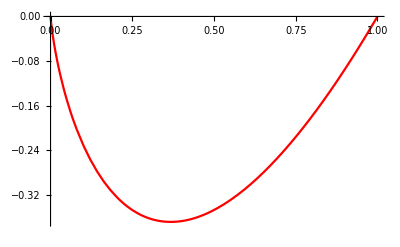

```mathematica
(*въвеждаме условието на задачата*)
Clear[x, a, b, y, points, f];
a=0.;b=1.;x=a;y=9.;
points={{x,y}};
f[x_,y_]:=y-Log[x^2+1]+(2x)/(x^2+1)+9;
(*точно решение*)
yt[x_]:=x Log[x];
(*съставяме мрежата*)
h=0.02;n=(b-a)/h;
Print["Мрежата е с n = ",n," и стъпка h = ",h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка е ",h^5]
Print["Теоретичната глобална грешка е ",h^4]
(*намираме неизвестните стойности за yi*)
For[i=0,i≤n,i++,
k1=h*f[x,y];
  k2=h*f[x+1/2 h,y+1/2 k1];
k3=h*f[x+1/2 h,y+1/2 k2];
  k4=h*f[x+h,y+k3];
Print["i = ",i," xi = ",x," yi = ",y," k1 = ",k1," k2 = ",k2," k3 = ",k3," k4 = ",k4," yточно = ",yt[x]," истинска грешка = ",Abs[y-yt[x]]//N];
y=y+1/6(k1+2 k2+2 k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt=Plot[yt[x],{x,a,b},PlotStyle->Red];
grp=ListPlot[points,PlotStyle->Black];
Show[gryt,grp]
```